## Algebraic Connectivity Functions

```mathematica
qmat[n_]:=Module[{q},
q=ConstantArray[0,{n,n-1}];
For[j=1,j≤n-1,j++,
q[[1;;j,j]]=1;
q[[j+1,j]]=-j;
q[[All,j]]=q[[All,j]]/Norm[q[[All,j]]];
];
N[q]
];
```

```mathematica
algcon[l_]:=Module[{n},
n=Length[l];
q=qmat[n];
Min[Eigenvalues[(1/2)*(Transpose[q].(l+Transpose[l]).q)]]
];
betacon[l_]:=Module[{n},
n=Length[l];
q=qmat[n];
Max[Eigenvalues[(1/2)*(Transpose[q].(l+Transpose[l]).q)]]
];
```

```mathematica
dom[n_]:=Module[{l},
l=ConstantArray[0,{n,n}];
For[i=1,i≤n,i++,
l[[i,i]]=n-i;
l[[i,i+1;;n]]=-1;
];
N[l]
];
```

### Algebraic Connectivity of Perfect Dominance Graph

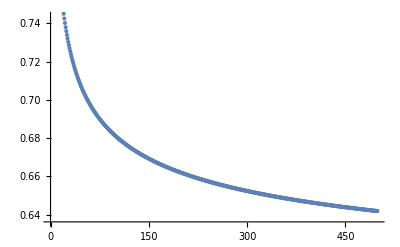

```mathematica
ListPlot[Table[algcon[dom[n]],{n,2,500}]]
```

## Algebraic Connectivity Inequalities

```mathematica
(* Graph Laplacians *)
l1=dom[6];
l2=N[{{2,-1,-1,0,0,0},{0,1,-1,0,0,0},{0,0,0,0,0,0},{0,0,0,2,-1,-1},{0,0,0,0,1,-1},{0,0,0,0,0,0}}];
l3=N[{{5,-1,-1,-1,-1,-1},{-1,5,-1,-1,-1,-1},{-1,-1,5,-1,-1,-1},{-1,-1,-1,5,-1,-1},{-1,-1,-1,-1,5,-1},{-1,-1,-1,-1,-1,5}}];
```

```mathematica
(* Lemma 3 *)
```

```mathematica
e1=Sort[Eigenvalues[(1/2)*(l1+Transpose[l1])],Less];
e2=Sort[Eigenvalues[(1/2)*(l2+Transpose[l2])],Less];
e3=Sort[Eigenvalues[(1/2)*(l3+Transpose[l3])],Less];
MatrixForm[{{"Graph","lambda1","AlgCon","lambda2", "lambda(n-1)","BetaCon","lambdan"},{"Dominance",e1[[1]],algcon[l1],e1[[2]],e1[[5]],betacon[l1],e1[[6]]},{"Disconnected",e2[[1]],algcon[l2],e2[[2]],e2[[5]],betacon[l2],e2[[6]]},{"Completely Connected",e3[[1]],algcon[l3],e3[[2]],e3[[5]],betacon[l3],e3[[6]]}}]
```

(Graph | lambda1 | AlgCon | lambda2 | lambda(n-1) | BetaCon | lambdan
Dominance | -0.892962 | 0.836553 | 1.04818 | 4.23536 | 5.16345 | 5.28564
Disconnected | -0.389229 | -0.389229 | -0.389229 | 2.24464 | 2.24464 | 2.24464
Completely Connected | 0. | 6. | 6. | 6. | 6. | 6.)

```mathematica
N[1/(2*Sqrt[6])+1/(2*Sqrt[2])]
```

0.557678